## Page-Wootters model: NN-level clock + 2-level system

```mathematica
NN= 32
```

32

```mathematica
T := DiagonalMatrix[Range[0,NN-1]]
```

```mathematica
MatrixForm[T]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 19 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 21 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 24 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 25 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 26 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 27 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 28 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 29 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 30 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 31)

```mathematica
F := FourierMatrix[NN]
```

```mathematica
Ω := F.T.F†
```

Hamiltonian in "ordinary" space

```mathematica
Hs := ⅈ{{0,1},{-1,0}}
```

```mathematica
MatrixForm[Hs]
```

(0 | ⅈ
-ⅈ | 0)

```mathematica
TeXForm[Hs]
```

"\\left(\n\\begin{array}{cc}\n 0 & i \\\\\n -i & 0 \\\\\n\\end{array}\n\\right)"

Matrix representation of eq. (1) in https://arxiv.org/abs/1504.04215 by Lloyd, Giovannetti and Maccone.
We turn it into numeric as treating  it symbolically onwards would be unfeasible.

```mathematica
J := N[KroneckerProduct[Ω,IdentityMatrix[2]] + KroneckerProduct[IdentityMatrix[NN],Hs]]
```

```mathematica
Chop[Eigenvalues[J]]
```

{32.,31.,30.,30.,29.,29.,28.,28.,27.,27.,26.,26.,25.,25.,24.,24.,23.,23.,22.,22.,21.,21.,20.,20.,19.,19.,18.,18.,17.,17.,16.,16.,15.,15.,14.,14.,13.,13.,12.,12.,11.,11.,10.,10.,9.,9.,8.,8.,7.,7.,6.,6.,5.,5.,4.,4.,3.,3.,2.,2.,1.,1.,-1.,0}

```mathematica
Eigenvalues[J][[40]]
```

12.

```mathematica
Eigenvalues[J][[41]]
```

11.

```mathematica
chosenEigenvector := Eigenvectors[J][[ 40]]

chosenEigenvectorB := Eigenvectors[J][[41]]
```

```mathematica
Normalization := Sqrt[Abs[chosenEigenvector[[1]]^2] + Abs[chosenEigenvector[[2]]^2] ]
```

```mathematica
NormalizationB := Sqrt[Abs[chosenEigenvectorB[[1]]^2] + Abs[chosenEigenvectorB[[2]]^2] ]

chosenEigenvectorNormalized  := chosenEigenvector / Normalization
```

```mathematica
chosenEigenvectorNormalizedB  = chosenEigenvectorB / NormalizationB
```

{-0.938878+0.00640243 ⅈ,0.299377-0.169824 ⅈ,0.501468-0.702168 ⅈ,-0.125361+0.489667 ⅈ,0.233524+0.718144 ⅈ,-0.390559-0.526498 ⅈ,-0.585152-0.207164 ⅈ,0.783971+0.0083447 ⅈ,0.401462-0.23804 ⅈ,-0.531014+0.707241 ⅈ,-0.0818027+0.294304 ⅈ,-0.282503-0.909332 ⅈ,-0.0173053-0.174341 ⅈ,0.934362+0.310279 ⅈ,-1.25607×10^-15+0.198819 ⅈ,-0.792316+0.576807 ⅈ,-0.169824-0.299377 ⅈ,-0.00640243-0.938878 ⅈ,0.489667+0.125361 ⅈ,0.702168+0.501468 ⅈ,-0.526498+0.390559 ⅈ,-0.718144+0.233524 ⅈ,0.0083447-0.783971 ⅈ,0.207164-0.585152 ⅈ,0.707241+0.531014 ⅈ,0.23804+0.401462 ⅈ,-0.909332+0.282503 ⅈ,-0.294304-0.0818027 ⅈ,0.310279-0.934362 ⅈ,0.174341-0.0173053 ⅈ,0.576807+0.792316 ⅈ,-0.198819+5.49532×10^-16 ⅈ,-0.938878+0.00640243 ⅈ,0.299377-0.169824 ⅈ,0.501468-0.702168 ⅈ,-0.125361+0.489667 ⅈ,0.233524+0.718144 ⅈ,-0.390559-0.526498 ⅈ,-0.585152-0.207164 ⅈ,0.783971+0.0083447 ⅈ,0.401462-0.23804 ⅈ,-0.531014+0.707241 ⅈ,-0.0818027+0.294304 ⅈ,-0.282503-0.909332 ⅈ,-0.0173053-0.174341 ⅈ,0.934362+0.310279 ⅈ,3.53271×10^-16+0.198819 ⅈ,-0.792316+0.576807 ⅈ,-0.169824-0.299377 ⅈ,-0.00640243-0.938878 ⅈ,0.489667+0.125361 ⅈ,0.702168+0.501468 ⅈ,-0.526498+0.390559 ⅈ,-0.718144+0.233524 ⅈ,0.0083447-0.783971 ⅈ,0.207164-0.585152 ⅈ,0.707241+0.531014 ⅈ,0.23804+0.401462 ⅈ,-0.909332+0.282503 ⅈ,-0.294304-0.0818027 ⅈ,0.310279-0.934362 ⅈ,0.174341-0.0173053 ⅈ,0.576807+0.792316 ⅈ,-0.198819+0. ⅈ}

```mathematica
probability := Abs[chosenEigenvectorNormalized ^2]
```

```mathematica
probabilityB := Abs[chosenEigenvectorNormalizedB^2]
```

```mathematica
probability
```

{0.716702,0.283298,0.771924,0.228076,0.785749,0.214251,0.756071,0.243929,0.687408,0.312592,0.590214,0.409786,0.479286,0.520714,0.371512,0.628488,0.283298,0.716702,0.228076,0.771924,0.214251,0.785749,0.243929,0.756071,0.312592,0.687408,0.409786,0.590214,0.520714,0.479286,0.628488,0.371512,0.716702,0.283298,0.771924,0.228076,0.785749,0.214251,0.756071,0.243929,0.687408,0.312592,0.590214,0.409786,0.479286,0.520714,0.371512,0.628488,0.283298,0.716702,0.228076,0.771924,0.214251,0.785749,0.243929,0.756071,0.312592,0.687408,0.409786,0.590214,0.520714,0.479286,0.628488,0.371512}

```mathematica
probabilityB
```

{0.881533,0.118467,0.744511,0.255489,0.570264,0.429736,0.38532,0.61468,0.217835,0.782165,0.0933066,0.906693,0.0306941,0.969306,0.0395291,0.960471,0.118467,0.881533,0.255489,0.744511,0.429736,0.570264,0.61468,0.38532,0.782165,0.217835,0.906693,0.0933066,0.969306,0.0306941,0.960471,0.0395291,0.881533,0.118467,0.744511,0.255489,0.570264,0.429736,0.38532,0.61468,0.217835,0.782165,0.0933066,0.906693,0.0306941,0.969306,0.0395291,0.960471,0.118467,0.881533,0.255489,0.744511,0.429736,0.570264,0.61468,0.38532,0.782165,0.217835,0.906693,0.0933066,0.969306,0.0306941,0.960471,0.0395291}

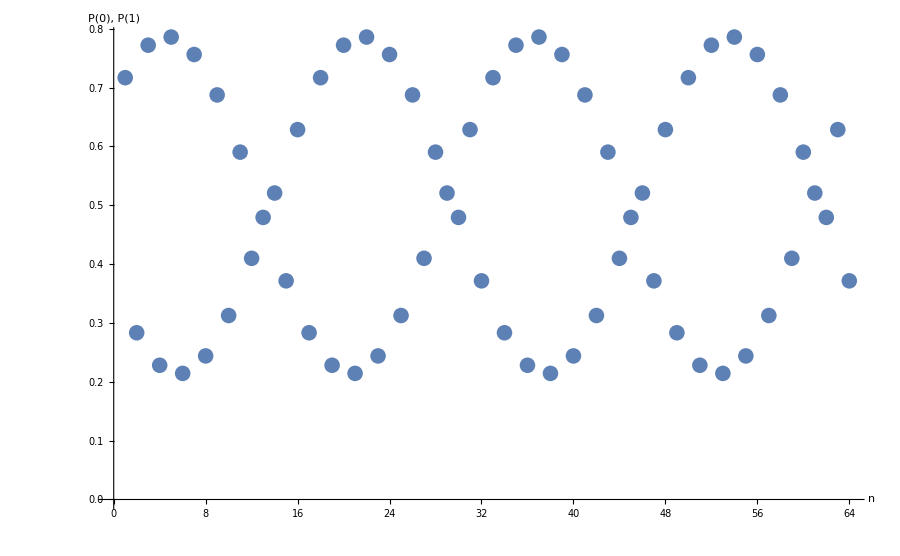

```mathematica
ListPlot[probability,
GridLines->{Range[0,NN*2, 2], Range[0,1,0.1]}, 
AxesLabel->{n, "P(0), P(1)"},
LabelStyle->Directive[16],
PlotMarkers->{Automatic,16},
ImageSize->900
]
```

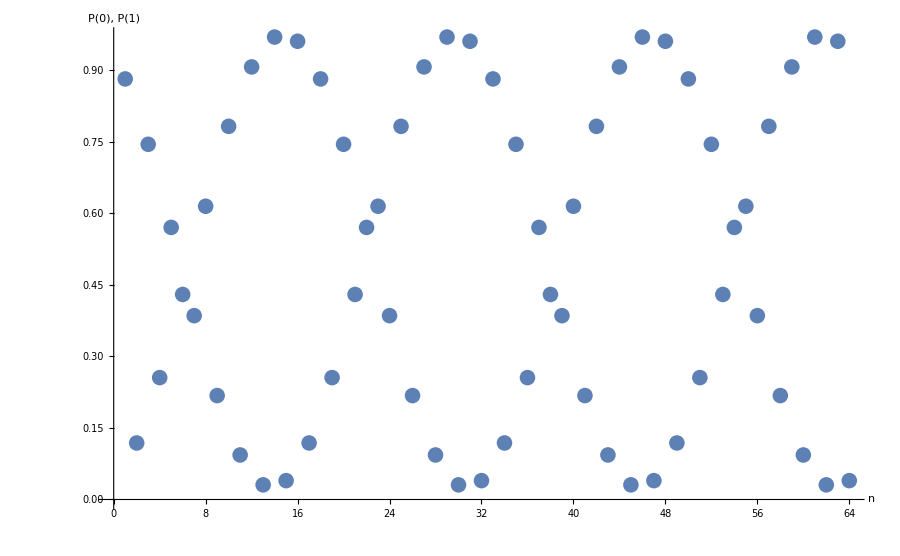

```mathematica
ListPlot[probabilityB, 
GridLines ->{Range[0,NN*2, 2], Range[0,1,0.1]},
AxesLabel->{n, "P(0), P(1)"},
LabelStyle->Directive[16],
PlotMarkers->{Automatic,16},
ImageSize->900
]
```

Consistency of PW with ordinary QM (discrete approximation):

```mathematica
chosenEigenvectorNormalizedB
```

{-0.938878+0.00640243 ⅈ,0.299377-0.169824 ⅈ,0.501468-0.702168 ⅈ,-0.125361+0.489667 ⅈ,0.233524+0.718144 ⅈ,-0.390559-0.526498 ⅈ,-0.585152-0.207164 ⅈ,0.783971+0.0083447 ⅈ,0.401462-0.23804 ⅈ,-0.531014+0.707241 ⅈ,-0.0818027+0.294304 ⅈ,-0.282503-0.909332 ⅈ,-0.0173053-0.174341 ⅈ,0.934362+0.310279 ⅈ,-1.25607×10^-15+0.198819 ⅈ,-0.792316+0.576807 ⅈ,-0.169824-0.299377 ⅈ,-0.00640243-0.938878 ⅈ,0.489667+0.125361 ⅈ,0.702168+0.501468 ⅈ,-0.526498+0.390559 ⅈ,-0.718144+0.233524 ⅈ,0.0083447-0.783971 ⅈ,0.207164-0.585152 ⅈ,0.707241+0.531014 ⅈ,0.23804+0.401462 ⅈ,-0.909332+0.282503 ⅈ,-0.294304-0.0818027 ⅈ,0.310279-0.934362 ⅈ,0.174341-0.0173053 ⅈ,0.576807+0.792316 ⅈ,-0.198819+5.49532×10^-16 ⅈ,-0.938878+0.00640243 ⅈ,0.299377-0.169824 ⅈ,0.501468-0.702168 ⅈ,-0.125361+0.489667 ⅈ,0.233524+0.718144 ⅈ,-0.390559-0.526498 ⅈ,-0.585152-0.207164 ⅈ,0.783971+0.0083447 ⅈ,0.401462-0.23804 ⅈ,-0.531014+0.707241 ⅈ,-0.0818027+0.294304 ⅈ,-0.282503-0.909332 ⅈ,-0.0173053-0.174341 ⅈ,0.934362+0.310279 ⅈ,3.53271×10^-16+0.198819 ⅈ,-0.792316+0.576807 ⅈ,-0.169824-0.299377 ⅈ,-0.00640243-0.938878 ⅈ,0.489667+0.125361 ⅈ,0.702168+0.501468 ⅈ,-0.526498+0.390559 ⅈ,-0.718144+0.233524 ⅈ,0.0083447-0.783971 ⅈ,0.207164-0.585152 ⅈ,0.707241+0.531014 ⅈ,0.23804+0.401462 ⅈ,-0.909332+0.282503 ⅈ,-0.294304-0.0818027 ⅈ,0.310279-0.934362 ⅈ,0.174341-0.0173053 ⅈ,0.576807+0.792316 ⅈ,-0.198819+0. ⅈ}

```mathematica
psi0 :=  chosenEigenvectorNormalizedB[[{1,2}]]
```

```mathematica
psi0
```

{-0.938878+0.00640243 ⅈ,0.299377-0.169824 ⅈ}

```mathematica
psi[t_] := MatrixExp[-ⅈ Hs t, psi0 ]
```

```mathematica
psi[t]
```

{(-0.938878+0.00640243 ⅈ) Cos[t]+(0.299377-0.169824 ⅈ) Sin[t],(0.299377-0.169824 ⅈ) Cos[t]+(0.938878-0.00640243 ⅈ) Sin[t]}

```mathematica
Abs[psi[t]]^2
```

{Abs[(-0.938878+0.00640243 ⅈ) Cos[t]+(0.299377-0.169824 ⅈ) Sin[t]]^2,Abs[(0.299377-0.169824 ⅈ) Cos[t]+(0.938878-0.00640243 ⅈ) Sin[t]]^2}

```mathematica
(Abs[psi[t]]^2)[[1]]
```

Abs[(-0.938878+0.00640243 ⅈ) Cos[t]+(0.299377-0.169824 ⅈ) Sin[t]]^2

```mathematica
Plot[Abs[(-0.9388782372790487+0.006402425881189263 ⅈ) Cos[t]+(0.2993765851207657-0.1698243939722771 ⅈ) Sin[t]]^2,{t,0,2π},
AxesLabel->{t, "P(0)"},
LabelStyle->Directive[16],
ImageSize->900
]
```

-Graphics-

```mathematica
(Abs[psi[t]]^2)[[2]]
```

Abs[(0.299377-0.169824 ⅈ) Cos[t]+(0.938878-0.00640243 ⅈ) Sin[t]]^2

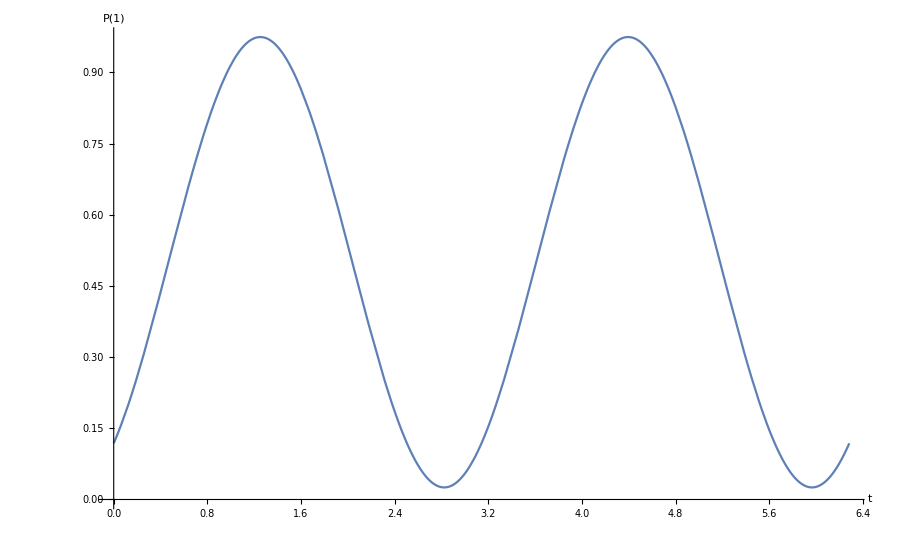

```mathematica
Plot[Abs[(0.2993765851207657-0.1698243939722771 ⅈ) Cos[t]+(0.9388782372790487-0.006402425881189263 ⅈ) Sin[t]]^2,{t,0,2π},
AxesLabel->{t, "P(1)"},
LabelStyle->Directive[16],
ImageSize->900
]
```

### Complex evolution of ψ (not just |ψ|^2)

```mathematica
psi[t][[1]]
```

(-0.938878+0.00640243 ⅈ) Cos[t]+(0.299377-0.169824 ⅈ) Sin[t]

```mathematica
psi[t][[2]]
```

(0.299377-0.169824 ⅈ) Cos[t]+(0.938878-0.00640243 ⅈ) Sin[t]

Let's do this manually - please note index count is 1, 2 but refers, respectively, to computational base elements |0>, |1> in ordinary Hilbert space

```mathematica
re0psi[t_] := (-0.938878 ) Cos[t] + (0.299377) Sin[t]
```

```mathematica
im0psi[t_] := (0.00640243) Cos[t] + (- 0.169824 ) Sin[t]
```

```mathematica
re1psi[t_] := (0.299377) Cos[t] + (0.938878) Sin[t]
```

```mathematica
im1psi[t_] := (- 0.169824) Cos[t] + (- 0.00640243) Sin[t]
```

```mathematica
zAxis := ParametricPlot3D[{0,0,t}, {t,0,2π}, PlotStyle->{Gray}]
```

```mathematica
psi0plot := ParametricPlot3D[{re0psi[t], im0psi[t], t}, {t, 0, 2π}, PlotStyle->{Red} ]
```

```mathematica
psi1plot := ParametricPlot3D[{re1psi[t], im1psi[t], t}, {t, 0, 2π}, PlotStyle->{Blue} ]
```

```mathematica
Show[zAxis, psi0plot,psi1plot, ImageSize->Medium,
AxesLabel->{Style[Re["<0,1|ψ>"], Bold], Style[Im["<0,1|ψ>"], Bold], Style[t, Bold]}
]
```

-Graphics3D-

```mathematica
pi = N[π]
```

3.14159

```mathematica
rephased[k_] := chosenEigenvectorNormalizedB [[k]] * Exp[-ⅈ*pi*11*(k-1)/NN]
```

```mathematica
rephased1[k_] := chosenEigenvectorNormalizedB [[k]] * Exp[-ⅈ*pi*11*(k-2)/NN]
```

```mathematica
scatter[k_] := {Re[ rephased[k]], Im[ rephased[k]], pi*(k-1)/NN}
```

```mathematica
scatter1[k_] := {Re[ rephased1[k]], Im[ rephased1[k]], pi*(k-2)/NN}
```

```mathematica
scatterPoints = Map[scatter, Range[1,2*NN, 2]]
```

{{-0.938878,0.00640243,0.},{-0.862432,-0.0268517,0.19635},{-0.752844,-0.0590739,0.392699},{-0.614324,-0.089026,0.589049},{-0.452196,-0.115557,0.785398},{-0.27269,-0.137647,0.981748},{-0.0827052,-0.154447,1.1781},{0.110458,-0.165312,1.37445},{0.299377,-0.169824,1.5708},{0.47679,-0.16781,1.76715},{0.635881,-0.159347,1.9635},{0.770535,-0.144761,2.15984},{0.875578,-0.124611,2.35619},{0.946973,-0.0996728,2.55254},{0.981977,-0.0709041,2.74889},{0.979243,-0.0394105,2.94524},{0.938878,-0.00640243,3.14159},{0.862432,0.0268517,3.33794},{0.752844,0.0590739,3.53429},{0.614324,0.089026,3.73064},{0.452196,0.115557,3.92699},{0.27269,0.137647,4.12334},{0.0827052,0.154447,4.31969},{-0.110458,0.165312,4.51604},{-0.299377,0.169824,4.71239},{-0.47679,0.16781,4.90874},{-0.635881,0.159347,5.10509},{-0.770535,0.144761,5.30144},{-0.875578,0.124611,5.49779},{-0.946973,0.0996728,5.69414},{-0.981977,0.0709041,5.89049},{-0.979243,0.0394105,6.08684}}

```mathematica
scatterPoints1 = Map[scatter1, Range[2,2*NN, 2]]
```

{{0.299377,-0.169824,0.},{0.47679,-0.16781,0.19635},{0.635881,-0.159347,0.392699},{0.770535,-0.144761,0.589049},{0.875578,-0.124611,0.785398},{0.946973,-0.0996728,0.981748},{0.981977,-0.0709041,1.1781},{0.979243,-0.0394105,1.37445},{0.938878,-0.00640243,1.5708},{0.862432,0.0268517,1.76715},{0.752844,0.0590739,1.9635},{0.614324,0.089026,2.15984},{0.452196,0.115557,2.35619},{0.27269,0.137647,2.55254},{0.0827052,0.154447,2.74889},{-0.110458,0.165312,2.94524},{-0.299377,0.169824,3.14159},{-0.47679,0.16781,3.33794},{-0.635881,0.159347,3.53429},{-0.770535,0.144761,3.73064},{-0.875578,0.124611,3.92699},{-0.946973,0.0996728,4.12334},{-0.981977,0.0709041,4.31969},{-0.979243,0.0394105,4.51604},{-0.938878,0.00640243,4.71239},{-0.862432,-0.0268517,4.90874},{-0.752844,-0.0590739,5.10509},{-0.614324,-0.089026,5.30144},{-0.452196,-0.115557,5.49779},{-0.27269,-0.137647,5.69414},{-0.0827052,-0.154447,5.89049},{0.110458,-0.165312,6.08684}}

```mathematica
Range[1,2*NN, 2]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63}

```mathematica
scatterPlot = ListPointPlot3D[scatterPoints, PlotStyle->{Red, PointSize[Large]}]
```

-Graphics3D-

```mathematica
scatterPlot1 = ListPointPlot3D[scatterPoints1, PlotStyle->{Blue, PointSize[Large]}]
```

-Graphics3D-

```mathematica
Show[zAxis, psi0plot,psi1plot,scatterPlot, scatterPlot1, ImageSize->Large,
AxesLabel->{Style[Re["<0,1|ψ>"], Bold], Style[Im["<0,1|ψ>"], Bold], Style[t, Bold]}
]
```

-Graphics3D-